```mathematica
ASym = 1;
deltaSym = 10;
rhoSym = 0.04;
kappa0 = 1;
kappa1 = 2;
kappa2 = 3;
kappa3 = 4;
vplus00 = 0.2405642552222122;
vplus02 = 2.440858868980155;
vplus10 = 0.0;
vplus12 = 2.495226145373615*10^-07;
vplus20 = 0.1013816051356955;
vplus22 = 0.7190196242297728;
vplus30 = 0.0;
vplus32 = 2.4952261453741994*10^-07;
```

```mathematica
f1 = control0^2*kappa0/2 - control0*deltaSym*(-value0 + vplus00) - control0*(ASym - control0 - control2) - control2*deltaSym*(-value0 + vplus02) + rhoSym*value0;
f2 = -control0*deltaSym*(-value1 + vplus10) - control2*deltaSym*(-value1 + vplus12) + rhoSym*value1;
f3 = -control0*deltaSym*(-value2 + vplus20) + control2^2*kappa2/2 - control2*deltaSym*(-value2 + vplus22) - control2*(ASym - control0 - control2) + rhoSym*value2;
f4 = -control0*deltaSym*(-value3 + vplus30) - control2*deltaSym*(-value3 + vplus32) + rhoSym*value3;
f5 = ASym - control0*kappa0 - 2*control0 - control2 + deltaSym*(-value0 + vplus00);
f6 = ASym - control0 - control2*kappa2 - 2*control2 + deltaSym*(-value2 + vplus22);
```

```mathematica
NSolve[{f1==0,f2==0,f3==0,f4==0,f5==0,f6==0},{value0,value1,value2,value3,control0,control2},Reals]
```

{{value0→6.98497,value2→-39.6934,control0→-52.6674,control2→91.5583,value1→5.87375×10^-7,value3→5.87375×10^-7},{value0→0.341869,value2→0.819151,control0→-0.00456483,control2→0.000650003,value1→1.90435×10^-6,value3→1.90435×10^-6}}

```mathematica
(*Flatten[{mu}~Join~Map[{#-mu≤0 , #+mu≥0}&,{f1, f2, f3, f4, f5, f6}]][[5]]*)
```

Bertini Solution (accurate to 10^-15!)

```mathematica
{f1, f2, f3, f4, f5, f6}/.{value0 -> 3.418687052310942*10^-01, value1 -> 1.904348981584601*10^-06, value2 -> 8.191511063304202*10^-01, value3 -> 1.904348981578778*10^-06, control0 -> -4.564834245544590*10^-03, control2 -> 6.500026478133097*10^-04}
```

{6.07153×10^-18,-1.49607×10^-19,2.08167×10^-17,-1.54941×10^-19,0.,4.44089×10^-15}

```mathematica
vals = Table[{Solve[Map[#1==0&,{f1,f2,f3,f4}]/.{control0 -> i, control2 -> j},{value0,value1,value2,value3}][[1]][[{1,3}]],i,j},{i,0,0.3,0.01},{j,0,0.3,0.01}];
```

```mathematica
firm1values = Transpose[MapThread[MapThread[List,{#1,#2}]&,{vals[[All,All,2]],vals[[All,All,1,1,2]]}]];
```

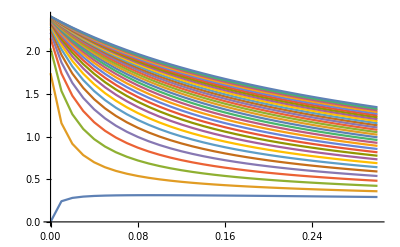

```mathematica
ListLinePlot[firm1values]
```

```mathematica
firm2values = MapThread[MapThread[List,{#1,#2}]&,{vals[[All,All,3]],vals[[All,All,1,2,2]]}];
```

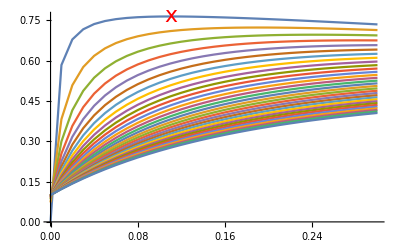

```mathematica
ListLinePlot[firm2values,Epilog->{Red,Text[Style["x",22],{0.110543939113671,0.7637476546729375}]}]
```

```mathematica
Solve[Map[#1==0&,{f1,f2,f3,f4,f6}]/.{control0 -> 0},{value0,value1,value2,value3,control2},PositiveReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{value0→2.35562,value1→2.40809×10^-7,value2→0.763748,value3→2.40809×10^-7,control2→0.110544}}